0.1

0.005

0.2

0.00166667

0.001

0.02

2

2

{{P[t]→InterpolatingFunction[…][t],Q[t]→InterpolatingFunction[…][t]}}

{{0,0},{0,120.},{20.,0},{2.85714,85.7143}}

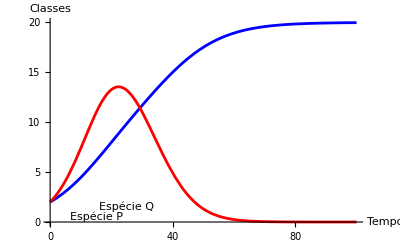

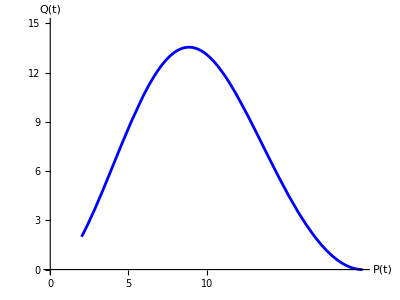

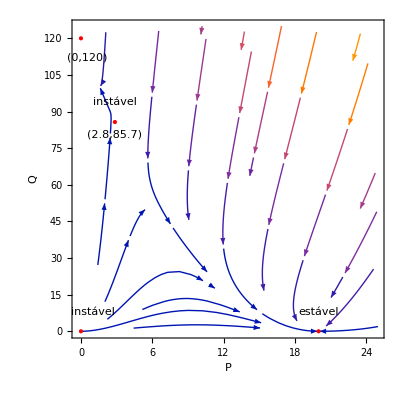

```mathematica
a=0.1
b=0.005
c=0.2
d=0.2/120
k=0.001
l=0.02
pini=2
qini=2


SolucaoNumerica=NDSolve[{P'[t]==(a-b*P[t]-k*Q[t])*P[t],Q'[t]==(c-d*Q[t]-l*P[t])*Q[t],P[0]==pini,Q[0]==qini},{P[t],Q[t]},{t,0,100}]


EqPontos={{0,0},{0,c/d},{a/b,0},{(c*k-a*d)/(k*l-b*d),(a*l-b*c)/(k*l-b*d)}}



PL1=Plot[Evaluate[{P[t],Q[t]}/.SolucaoNumerica],{t,0,100},PlotRange->{0,20},PlotStyle->{{Blue,Thickness[0.005]},{Red,Thickness[0.005]},{DarkerGreen,Thickness[0.005]}},Ticks->{{0,20,40,60,80,100},{0,5,10,15,20}},AxesLabel->{Tempo,Classes},LabelStyle->{Medium,Black,Bold},Epilog->{Text["StyleBox[\"Espécie Q\", \"Text\",FontColor->RGBColor[1, 0, 0]]",{25,1.5}],Text["StyleBox[\"Espécie\", \"Text\",FontColor->RGBColor[0., 0., 1.]]StyleBox[\" \", \"Text\",FontColor->RGBColor[0., 0., 1.]]StyleBox[\"P\", \"Text\",FontColor->RGBColor[0., 0., 1.]]",{15,0.5}]} ]


PL2=ParametricPlot[Evaluate[{P[t],Q[t]}/.SolucaoNumerica],{t,0,100},PlotRange->{{0,20},{0,15}},PlotStyle->{{Blue,Thickness[0.005]},{Red,Thickness[0.005]},{DarkerGreen,Thickness[0.005]}},Ticks->{{0,5,10,},{0,3,6,9,12,15}},AxesLabel->{"P(t)","Q(t)"},LabelStyle->{Medium,Black,Bold} ]

StreamPlot[{(a-b*P-k*Q)*P,(c-d*Q-l*P)*Q},{P,-0.25,25},{Q,-0.25,125},FrameLabel->{P,Q}, StreamScale->1,StreamStyle->{Arrowheads[Small],RGBColor[0,0,1]},
Epilog->{{PointSize[Large],Red,Point[EqPontos]},Text["(0,0)",{0,-5}],Text["(0,120)",{0.5,-8+c/d}],Text["(20,0)",{0+a/b,-5}],Text["(2.8,85.7)",{0+(c*k-a*d)/(k*l-b*d),-5+(a*l-b*c)/(k*l-b*d)}],Text["estável",{1,8+c/d}],Text["estável",{0+a/b,8}],Text["instável",{1,8}],Text["instável",{0+(c*k-a*d)/(k*l-b*d),8+(a*l-b*c)/(k*l-b*d)}]}]
```